```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\robin\Google Drive\Master's thesis

```mathematica
exportAndDraw[name_,expression_]:=(Export[name,expression];expression)
```

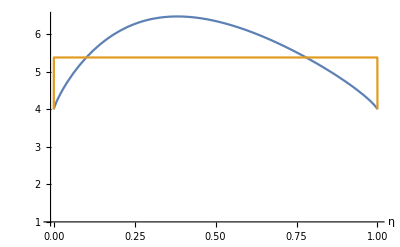

```mathematica
exportAndDraw["binomial-bound.pdf",Plot[{4((1-η)^(1-1/η)/η)^(η/(η+1)),If[η≤0.00001||η≥.99999,4,5.3793]},{η,0,1},PlotRange->{1,4GoldenRatio},
AxesLabel->{Style["η",FontFamily->"Cambria Math",FontSize->12]},
AxesOrigin->{-.01,1}]]
```

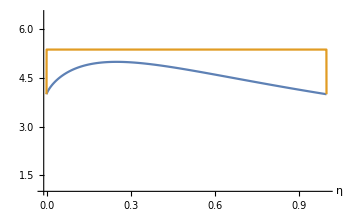

```mathematica
exportAndDraw["spc-bound.pdf",
Plot[{4^(1/(η+1))(η+1)/η^(η/(η+1)),If[η≤0.00001||η≥.99999,4,5.3793]},{η,0,1},PlotRange->{1,4GoldenRatio},AxesLabel->{Style["η",FontFamily->"Cambria Math",FontSize->12]},
AxesOrigin->{-.01,1}]]
```

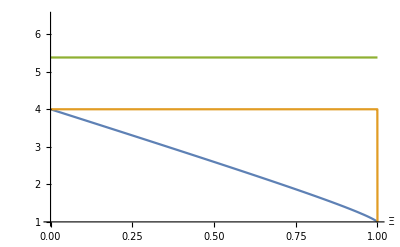

```mathematica
exportAndDraw["convexity-bound.pdf",
Plot[{(1-Ξ)^(Ξ-1)/(2-Ξ)^(Ξ-2),If[Ξ≥.99999,1,4],5.3793},{Ξ,0,1},PlotRange->{1,4GoldenRatio},AxesLabel->{Style["Ξ",Italic,FontFamily->"Cambria Math",FontSize->12]}]]
```

```mathematica
ClearAll[spc];
spc[a_Integer,a_Integer]:=spc[a,a]=CatalanNumber[a];
spc[a_Integer,b_Integer]:=spc[a,b]=Sum[spc[i,i]spc[a-i-1,b-i],{i,0,b}];
```

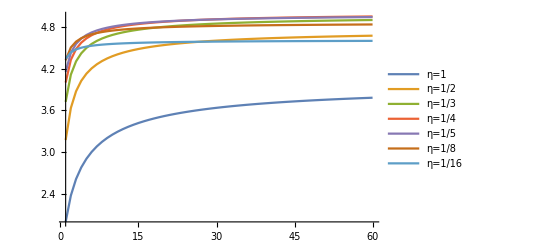

```mathematica
exportAndDraw["spc-asymptotics.pdf",
DiscretePlot[Evaluate@Table[{(4^(γ b)spc[γ b,b])^(1/((γ+1) b))},{γ,{1,2,3,4,5,8,16}}],{b,1,60},PlotRange->Full,Filling->None,Joined->True,PlotLegends->{Table[Style[If[γ==1,"η=1",StringReplace["η=1/γ","γ"->ToString[γ]]],FontFamily->"Cambria Math",FontSize->12],{γ,{1,2,3,4,5,8,16}}]},
AxesLabel->{Style["b",Italic,FontFamily->"Cambria Math",FontSize->12]}]]
```

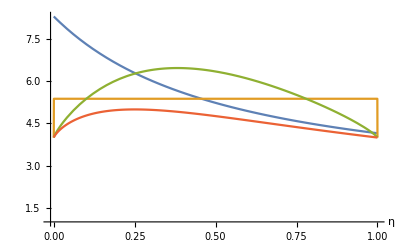

```mathematica
ϑ=1+Zeta[3/2]/√π-1/3(4 √(2/π)-2);
exportAndDraw["spc-zeta-bound.pdf",Plot[{4^(1/(1+η))ϑ,If[η≤0.00001||η≥.99999,4,5.3793],4((1-η)^(1-1/η)/η)^(η/(η+1)),4^(1/(η+1))(η+1)/η^(η/(η+1))},{η,0,1},PlotRange->{1,4ϑ},AxesLabel->{Style["η",FontFamily->"Cambria Math",FontSize->12]},
AxesOrigin->{-.01,1}]]
```